```mathematica
g=9.81;
l=100;(*Pool length*)
h=2;(*Pool depth*)
tMax=80;
meetDist=90;
windupTime[a_]:=1.5a/√((a g)/(2π)Tanh[(2π h)/a]);
travelTime[a_]:=0.5windupTime[a]+meetDist/√((a g)/(2π)Tanh[(2π h)/a]);
hanWindow[x_,p_]:=HannWindow@((x-p/2)/p);
composeBoundary[waves_]:=Module[{periods},
periods=Array[windupTime[waves[[1,#]]]&,Length[waves[[1]]]];
Return[Total[Array[Sin[(2π)/(1.5periods[[#]])(time-waves[[2,#]])]hanWindow[time-waves[[2,#]],1.5periods[[#]]]&,Length[waves[[1]]]]]];
];
calcLengths[meetTime_,numWaves_Integer,timeWait_]:=Module[{resLength,waitTimes,lag,idx,waveRoot},
resLength=Table[0.0,numWaves];
waitTimes=Table[0.0,numWaves];
lag=0.0;

For[idx=1,idx≤numWaves,idx++,
waveRoot=FindRoot[meetTime-lag==travelTime[x],{x,0.001}];
resLength[[idx]]=waveRoot[[1,2]];
waitTimes[[idx]]=lag;
lag=lag+timeWait+windupTime[resLength[[idx]]]
];

Return[{resLength,waitTimes}];
];
```

{{5.04627,9.27294},{0.,5.81019}}

{1.81019,2.60492}

{1.81019,2.60492}

{35.,35.}

HannWindow[0.255926 (-7.76388+time)] Sin[1.60803 (-5.81019+time)]+HannWindow[0.368285 (-1.35764+time)] Sin[2.314 (0.+time)]

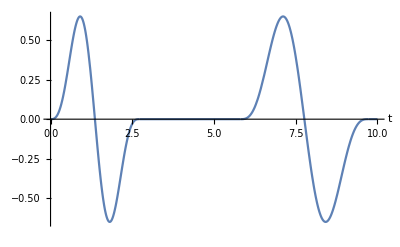

```mathematica
r=calcLengths[35,2,4.0]
periods=Array[r[[1,#]]/(√((r[[1,#]]g)/(2π)Tanh[(2π h)/r[[1,#]]]))&,Length[r[[1]]]]
Array[windupTime[r[[1,#]]]&,Length[r[[1]]]]
Array[travelTime[r[[1,#]]]+r[[2,#]]&,Length[r[[1]]]]

func=composeBoundary[r]
Plot[func,{time,0,10},AxesLabel->{"t"},PlotRange->All]
```

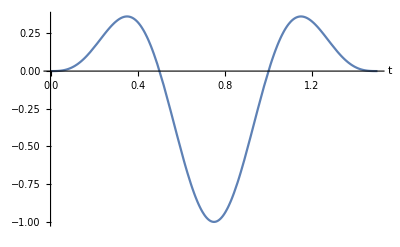

```mathematica
Plot[{
Sin[2π(x-r[[2,1]])]hanWindow[x,1.5],
},{x,0,1.5},AxesLabel->{"t"}]
```

```mathematica
t=HannWindow@0.1
```

0.904508